ANALYSIS OF EBOLA EPIDERMIC IN WEST AFRICA
                                     VIVIAN J. GOSHASHY

Importing Ebola Dataset

```mathematica
Ebola=Import["C:\\Users\\vivia\\Documents\\EBOLA\\Computer program\\Ebola from 2014 to 2016.csv", "Dataset", "HeaderLines"-> 1];
```

Replacing missing values in the dataset with 0

```mathematica
Ebola1=Ebola[All,{"Country","Date", "Days","Number of suspected cases", "Number of probable cases", "Number of confirmed cases","Number of confirmed, probable and suspected cases","Number of suspected deaths","Number of probable deaths","Number of confirmed deaths","Number of confirmed, probable and suspected deaths"}]/.""->0
```

Dataset[<>]

Filtering Data by Country

Sierra Leone

```mathematica
SL =Select[Ebola1, #Country == "Sierra Leone"&];
```

Create new datasets

Number of confirmed cases Dataset

```mathematica
SL1 = SL[All, {"Days", "Number of confirmed cases"}];
```

Converting SL1 dataset to List

```mathematica
time = Normal[SL1[[All,"Days"]]];
Susp = Normal[SL1[[All, "Number of confirmed cases"]]];
SL2 = Transpose[{time,Susp}];
```

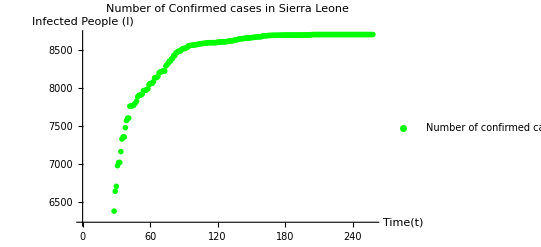

```mathematica
plot1=ListPlot[SL2,PlotStyle->{Green,PointSize[0.01]},PlotLegends->{"Number of confirmed cases"},PlotStyle->Black,AxesLabel->{"Time(t)","Infected People (I)"},PlotLabel->"Number of Confirmed cases in Sierra Leone"]
```

Number of confirmed deaths Dataset

```mathematica
SL01 = SL[All, {"Days", "Number of confirmed deaths"}];
```

Converting SL01 dataset to List

```mathematica
time = Normal[SL01[[All,"Days"]]];
Susp = Normal[SL01[[All, "Number of confirmed deaths"]]];
SL02 = Transpose[{time,Susp}];
```

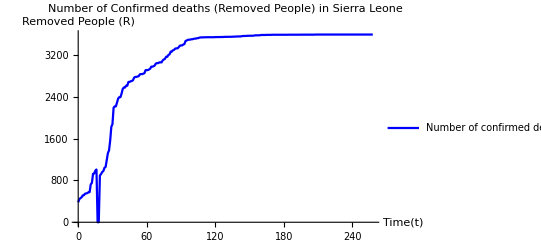

```mathematica
plot01=ListLinePlot[SL02,PlotStyle->{Blue,PointSize[0.01]},PlotLegends->{"Number of confirmed deaths"},PlotStyle->Black,AxesLabel->{"Time(t)","Removed People (R)"},PlotLabel->"Number of Confirmed deaths (Removed People) in Sierra Leone"]
```

Number of Suspected cases Dataset

```mathematica
SL001 = SL[All, {"Days", "Number of suspected cases"}];
```

Converting SL001 dataset to List

```mathematica
time = Normal[SL001[[All,"Days"]]];
Susp = Normal[SL001[[All, "Number of suspected cases"]]];
SL002 = Transpose[{time,Susp}];
```

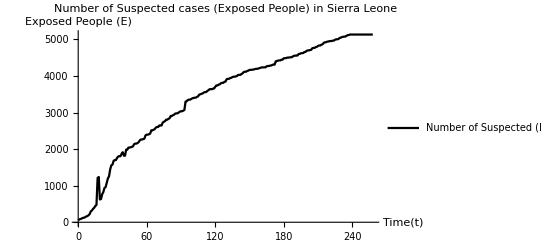

```mathematica
plot001=ListLinePlot[SL002,PlotStyle->{Black,PointSize[0.01]},PlotLegends->{"Number of Suspected (Exposed) cases"},PlotStyle->Black,AxesLabel->{"Time(t)","Exposed People (E)"},PlotLabel->"Number of Suspected cases (Exposed People) in Sierra Leone"]
```

ORDINARY DIFFERENTIAL EQUATION

SIR Model

```mathematica
Graph[{𝒮->ℐ,ℐ->ℛ},
VertexShapeFunction->Function[{xy,v,wh},Inset[Framed[Style[v,Black,18],Background->LightBlue],xy]],
EdgeLabels->{
𝒮->ℐ->Placed[Style[ α,Black,18],0.5],
ℐ->ℛ->Placed[Style[λ,Black,18],0.5]
},
PerformanceGoal->"Quality",
ImageSize->450
]
```

-Graphics-

Estimating parameters using the number of confirmed cases dataset

345323.

| Estimate | Standard Error | t-Statistic | P-Value
alpha | 8.6293×10^-6 | 1.5×10^-7 | 57.5287 | 8.41574×10^-149
lambda | 0.000943924 | 0.0000340061 | 27.7575 | 2.64316×10^-79

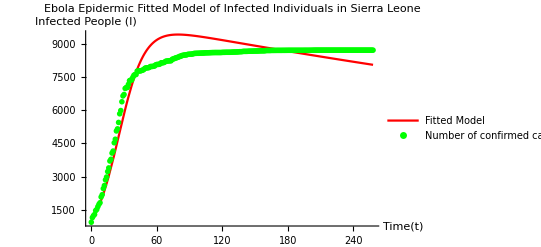

```mathematica
mymodel[alpha_?NumberQ,lambda_?NumberQ]:=Module[{S,I1,R1,t},First[I1/. NDSolve[{S'[t]==-alpha*S[t]*I1[t],I1'[t]==alpha*S[t]*I1[t]-lambda*I1[t],R1'[t]==lambda*I1[t],S[0]==9000,I1[0]==1000,R1[0]==0},{S,I1,R1},{t,0,258}]]]
myfit=NonlinearModelFit[SL2,mymodel[alpha,lambda][t],{{alpha,0.000005},{lambda,0.0000001}},t];
myfit["EstimatedVariance"]
myfit["ParameterTable"]
plotfit1=Plot[myfit[t],{t,0,258},PlotRange->All,AxesOrigin->{0,0},PlotLegends->{"Fitted Model"},PlotStyle->Red,AxesLabel->{"Time(t)","Infected People (I)"},PlotLabel->"Ebola Epidermic Fitted Model of Infected Individuals in Sierra Leone"];
Show[plotfit1,plot1]
```

Obtain the residuals and plot them for each data point

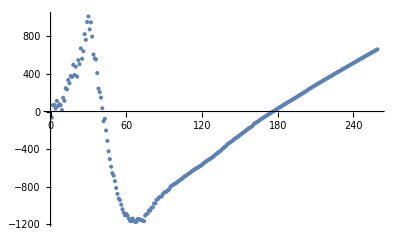

```mathematica
ListPlot[myfit["FitResiduals"]]
```

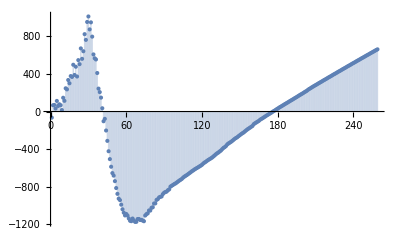

```mathematica
myfit["FitResiduals"];
ListPlot[%,Filling->Axis]
```

Estimating parameters using the number of confirmed deaths dataset

186681.

| Estimate | Standard Error | t-Statistic | P-Value
alpha | 0.000052571 | 3.4841×10^-6 | 15.0888 | 2.85118×10^-37
lambda | -0.00263093 | 0.0000576383 | -45.6455 | 2.76358×10^-125

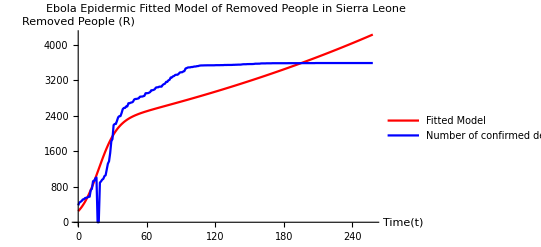

```mathematica
mymodel[alpha_?NumberQ,lambda_?NumberQ]:=Module[{S,I1,R1,t},First[I1/. NDSolve[{S'[t]==-alpha*S[t]*I1[t],I1'[t]==alpha*S[t]*I1[t]-lambda*I1[t],R1'[t]==lambda*I1[t],S[0]==2000,I1[0]==250,R1[0]==0},{S,I1,R1},{t,0,258}]]]
myfit1=NonlinearModelFit[SL02,mymodel[alpha,lambda][t],{{alpha,0.000005},{lambda,0.0000001}},t];
myfit1["EstimatedVariance"]
myfit1["ParameterTable"]
plotfit01=Plot[myfit1[t],{t,0,258},PlotRange->All,AxesOrigin->{0,0},PlotLegends->{"Fitted Model"},PlotStyle->Red,AxesLabel->{"Time(t)","Removed People (R)"},PlotLabel->"Ebola Epidermic Fitted Model of Removed People in Sierra Leone"];
Show[plotfit01,plot01]
```

Obtain the residuals and plot them for each data point

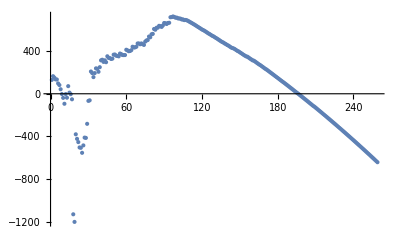

```mathematica
ListPlot[myfit1["FitResiduals"]]
```

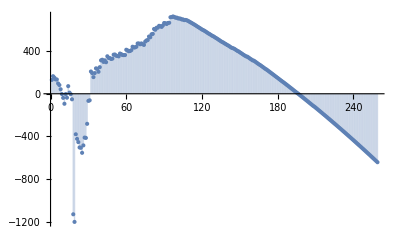

```mathematica
myfit1["FitResiduals"];
ListPlot[%,Filling->Axis]
```

Guinea

```mathematica
Guinea =Select[Ebola1, #Country == "Guinea"&];
```

Create new datasets

Number of confirmed cases Dataset

```mathematica
Guinea1 = Guinea[All, {"Days", "Number of confirmed cases"}];
```

Converting Guinea1 dataset to List

```mathematica
time = Normal[Guinea1[[All,"Days"]]];
Susp = Normal[Guinea[[All, "Number of confirmed cases"]]];
Guinea2 = Transpose[{time,Susp}];
```

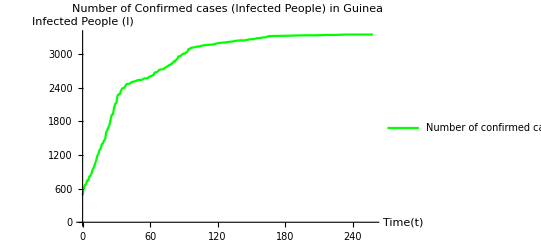

```mathematica
plot1=ListLinePlot[Guinea2,PlotStyle->{Green,PointSize[0.01]},PlotLegends->{"Number of confirmed cases"},PlotStyle->Black,AxesLabel->{"Time(t)","Infected People (I)"},PlotLabel->"Number of Confirmed cases (Infected People) in Guinea"]
```

Number of confirmed deaths Dataset

```mathematica
Guinea01 = Guinea[All, {"Days", "Number of confirmed deaths"}];
```

Converting Guinea1 dataset to List

```mathematica
time = Normal[Guinea01[[All,"Days"]]];
Susp = Normal[Guinea01[[All, "Number of confirmed deaths"]]];
Guinea02 = Transpose[{time,Susp}];
```

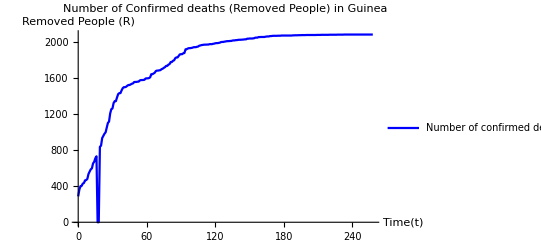

```mathematica
plot01=ListLinePlot[Guinea02,PlotStyle->{Blue,PointSize[0.01]},PlotLegends->{"Number of confirmed deaths"},PlotStyle->Black,AxesLabel->{"Time(t)","Removed People (R)"},PlotLabel->"Number of Confirmed deaths (Removed People) in Guinea"]
```

Number of suspected cases Dataset

```mathematica
Guinea001 = Guinea[All, {"Days", "Number of suspected cases"}];
```

Converting Guinea1 dataset to List

```mathematica
time = Normal[Guinea01[[All,"Days"]]];
Susp = Normal[Guinea001[[All, "Number of suspected cases"]]];
Guinea002 = Transpose[{time,Susp}];
```

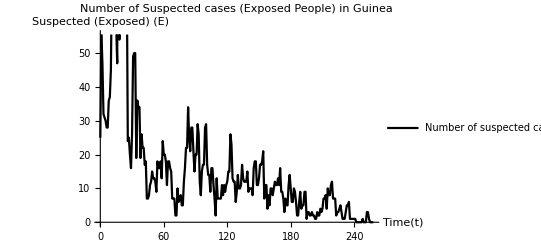

```mathematica
plot001=ListLinePlot[Guinea002,PlotStyle->{Black,PointSize[0.01]},PlotLegends->{"Number of suspected cases"},PlotStyle->Black,AxesLabel->{"Time(t)","Suspected (Exposed) (E)"},PlotLabel->"Number of Suspected cases (Exposed People) in Guinea"]
```

ORDINARY DIFFERENTIAL EQUATION

SIR Model

```mathematica
Graph[{𝒮->ℐ,ℐ->ℛ},
VertexShapeFunction->Function[{xy,v,wh},Inset[Framed[Style[v,Black,18],Background->LightBlue],xy]],
EdgeLabels->{
𝒮->ℐ->Placed[Style[ α,Black,18],0.5],
ℐ->ℛ->Placed[Style[λ,Black,18],0.5]
},
PerformanceGoal->"Quality",
ImageSize->450
]
closeCellGroup[]
```

-Graphics-

closeCellGroup[]

Estimating parameters using the number of confirmed cases dataset

68759.6

| Estimate | Standard Error | t-Statistic | P-Value
alpha | 9.24465×10^-6 | 1.52882×10^-7 | 60.4691 | 5.53045×10^-154
lambda | 0.00154127 | 0.0000459407 | 33.5491 | 6.92092×10^-96

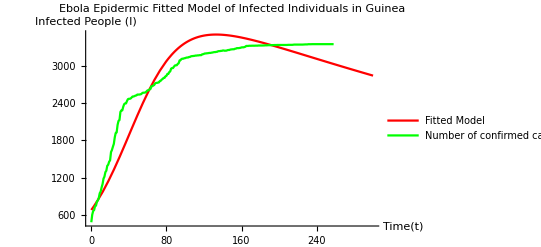

```mathematica
mymodel[alpha_?NumberQ,lambda_?NumberQ]:=Module[{S,I1,R1,t},First[I1/. NDSolve[{S'[t]==-alpha*S[t]*I1[t],I1'[t]==alpha*S[t]*I1[t]-lambda*I1[t],R1'[t]==lambda*I1[t],S[0]==3500,I1[0]==680,R1[0]==0},{S,I1,R1},{t,0,300}]]]
myfit2=NonlinearModelFit[Guinea2,mymodel[alpha,lambda][t],{{alpha,0.000005},{lambda,0.0000001}},t];
myfit2["EstimatedVariance"]
myfit2["ParameterTable"]
plotfit1=Plot[myfit2[t],{t,0,300},PlotRange->All,AxesOrigin->{0,0},PlotLegends->{"Fitted Model"},PlotStyle->Red,AxesLabel->{"Time(t)","Infected People (I)"},PlotLabel->"Ebola Epidermic Fitted Model of Infected Individuals in Guinea"];
Show[plotfit1,plot1]
```

Obtain the residuals and plot them for each data point

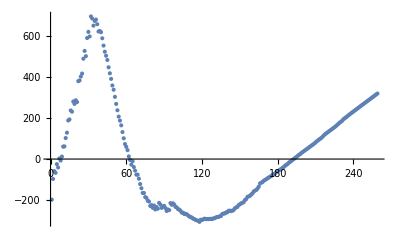

```mathematica
ListPlot[myfit2["FitResiduals"]]
```

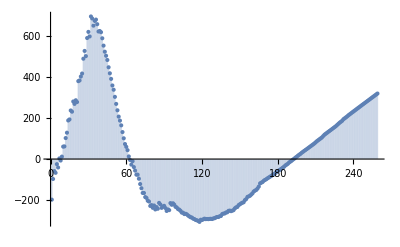

```mathematica
myfit2["FitResiduals"];
ListPlot[%,Filling->Axis]
```

Estimating parameters using the number of confirmed deaths dataset

20520.1

| Estimate | Standard Error | t-Statistic | P-Value
alpha | 0.0000171795 | 2.76116×10^-7 | 62.2184 | 5.78882×10^-157
lambda | 0.000989404 | 0.0000390071 | 25.3647 | 6.34142×10^-72

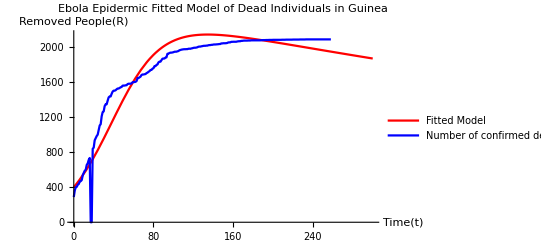

```mathematica
mymodel[alpha_?NumberQ,lambda_?NumberQ]:=Module[{S,I1,R1,t},First[I1/. NDSolve[{S'[t]==-alpha*S[t]*I1[t],I1'[t]==alpha*S[t]*I1[t]-lambda*I1[t],R1'[t]==lambda*I1[t],S[0]==2000,I1[0]==400,R1[0]==0},{S,I1,R1},{t,0,300}]]]
myfit3=NonlinearModelFit[Guinea02,mymodel[alpha,lambda][t],{{alpha,0.000005},{lambda,0.0000001}},t];
myfit3["EstimatedVariance"]
myfit3["ParameterTable"]
plotfit01=Plot[myfit3[t],{t,0,300},PlotRange->All,AxesOrigin->{0,0},PlotLegends->{"Fitted Model"},PlotStyle->Red,AxesLabel->{"Time(t)","Removed People(R)"},PlotLabel->"Ebola Epidermic Fitted Model of Dead Individuals in Guinea"];
Show[plotfit01,plot01]
```

Obtain the residuals and plot them for each data point

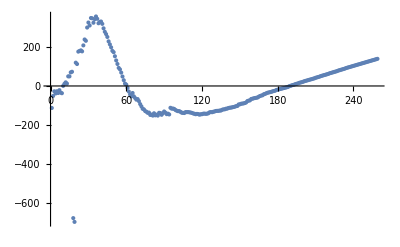

```mathematica
ListPlot[myfit3["FitResiduals"]]
```

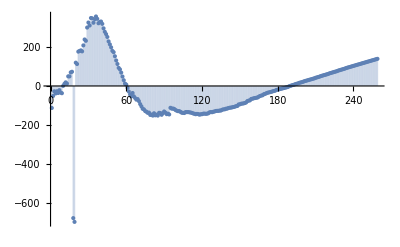

```mathematica
myfit3["FitResiduals"];
ListPlot[%,Filling->Axis]
```